Abstract: We investigate connections between FQFT and the Wolfram Model by looking at possible notions of cobordisms within graphs and hypergraphs. In addition, we seek to construct category diagrams with a multiway functorial QFT and look at Lorentzian spacetime as objects, morphisms as causal relations and use category algebra as observables assigned to a localized subgraph. The project seeks in this way to also develop a connection with AQFT.

## Functorial Quantum Field Theory

FQFT  is an approach for providing a precise mathematical formulation of QFT through concepts and ideas from category theory. The fundamental idea is to translate statements about the path integral and the S-matrix into statements about functors. One hopes in this way to create an equivalence between the consistency conditions that these objects must follow in QFT and simple properties that the functor, suitably chosen to represent quantum propagation, will satisfy. More specifically, we are interested in functors from categories whose objects are (n − 1)- dimensional manifolds and whose morphisms are n-dimensional cobordisms between these to a category of vector spaces.

						Z : nCob ⟶ Vect

It can be shown that the functor chosen obey the axioms of TQFT originally proposed by Atiyah [1] and reproduced below:

1. Z is functorial with respect to orientation preserving diffeomorphisms of Σ (a n-dimensional manifold) and M (the boundary of Σ).
2. Z is involutory, i.e. Z(Σ*) = Z(Σ)* where Σ* is Σ with opposite orientation and Z(Σ)* denotes the dual module.
3. Z is multiplicative.
4. Z(ϕ) = Λ (the ground ring) for the d-dimensional empty manifold and Z(ϕ) = 1 for the (n + 1)-dimensional empty manifold.
5. Z(M*) = Z(M) (the hermitian axiom). If  so that Z(M) can be viewed as a linear transformation between hermitian vector spaces, then this is equivalent to Z(M*) being the adjoint of Z(M).

Intuitively, we can think of the functor as assigning space to a vector space of quantum states. We see then how FQFT allows us to reduce the apparent complexity of QFT and formalize the concept of the quantum propagator acting on the space of quantum states  via the Atiyah-Segal axioms. As a further motivating example, consider the case of the Schrödinger picture in FQFT.

### The Schrödinger Picture in FQFT

In the Schrödinger picture of quantum mechanics operators are fixed and states evolve through time via the action of the time evolution propagator U(,). In the language of FQFT this corresponds to the functor:
						
						U :  1Cob  ⟶ Vect

mapping the category of time instants, whose morphisms are time intervals, to the category of Vector spaces:
                                                    
 	-Graphics-

We note that this preserves the notion of locality in quantum mechanics, which  corresponds to the condition that if  <  < , then:

					U(,) = U(,)∘U(,)

We can turn this statement into a statement about functoriality. Our system is such that composition within the instants of time category correspond to the concatenation of time intervals and the homomorphisms in Vect in turn can also be composed so that the functor property is satisfied.

### FQFT as the dual of AQFT

The relation between FQFT and AQFT is captured by the following endomorphism functor:
							
 					End : Vect → Algebras
  
 sending each vector space to its algebra of endomorphisms and each isomorphism of vector space to the corresponding isomorphism of algebras.
As it has been shown, this functor satisfies the axioms of AQFT in one and two dimensions [2].
We note for instance, how it codifies the passage from the Schrodinger picture to the Heisenberg picture:
		
	

The functor translates the unitary transformation between representations by sending any operator A on E to  .

## Relation to the Wolfram Model

In the Wolfram model space is represented by spatial hypergraphs which evolve according to an update rule:


-Graphics-
	Fig.1: Evolution history for the rule {{x, y} , {y, z}} → {{w, y} , {y, z} , {z, w} , {x, w}}. Extracted from [3].

The arbitrariness involved in the application of the rule can be fixed when one considers the notion of causality within the multiway evolution of the graph and construct a causal network which in turn gives an approximation to the Lorentzian manifold structure of special relativity.

-Graphics-
	Fig.2: Multiway evolution for the rule shown previously and its causal graph which in the limit should correspond to a Lorentzian manifold.
    
Looking for cobordisms within this system translates to identifying  morphisms as disjoint unions of space-like separated events. A less defined notion of cobordism exist within spatial hypergraphs as well. We can look for particular rules exhibiting splitting behaviour and apply it to graphs, subsequently investigating its evolution behavior.

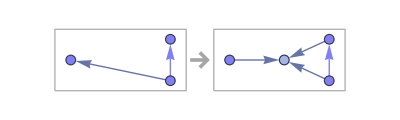

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}]]
```

The function below allows us to apply the rule to all vertices of a given hypergraph:

```mathematica
SimpleCobordism[rule_,init_,t_,tc_,a_]:=Block[{b},
b=a;
If[b==1,Return[ResourceFunction["HypergraphToGraph"][SetReplace[ResourceFunction["WolframModel"][rule,init,t,"FinalState"],{{v1_,v2_}}:>Module[{v3},{{v1,v3},{v3,v2}}],tc]]]];
If[b==2,Return[ResourceFunction["HypergraphToGraph"][SetReplace[ResourceFunction["WolframModel"][rule,init,t,"FinalState"],{{v1_,v2_}}:>Module[{v3=2},{{v3 v1,v3 v2}}],tc]]]];
]
```

```mathematica
SimpleCobordism[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},8,1000,1]
```

-Graphics-

The multiway graph also encodes the Vect/Hilb category as was rigorously shown by Gorard through the formalism of ZX calculus [4]. The evolution edges provide linear isomorphisms  and the parallel branches provide a monoidal product. Consider for instance the multiway evolution graph:

-Graphics-
	Fig.3: Foliation of  the multiway evolution graph for the rule shown previously and one of its branchial graphs. Extracted from [4].

Each state vertex within the multiway evolution graph corresponds to a different pure state for the universe and each branchial graph is indicating the instantaneous superposition of certain eigenstates at a given moment of time. With the evolution of the multiway system from one branchlike hypersurface to the next we are effectively performing a unitary evolution of the wave function. In the continuum limit of an infinitely large multiway system therefore, the branchlike hypersurfaces embedded within a particular foliation of the multiway graph correspond to complex projective Hilbert spaces. With these notions in mind we can seek to construct the equivalent of a 1D-QFT.

## 1D TQFT

We start with the causal graph for the rule {"A"→"BBB","BB"→"A"} with initial state "A". The points which are space-like separated with respect to a certain origin vertex can be found with the help of the function:

```mathematica
findSpacelikeSeparated[causalGraph_, origin_] := 
  Complement[VertexList[causalGraph], 
   Union[VertexInComponent[causalGraph, origin], VertexOutComponent[causalGraph, origin]]];
```

-Graphics-
	Fig.4:  Causal network for the rule cited above with space-like separated points highlighted in blue. The points highlighted share no causal edges and as such are all space-like separated.
    
In the 1D case we have a 1Cob in the multiway given by the disjoint union of vertices, this correspond to constructing paths within the causal graph of the form pictured on the figure on the right above.

The Vect category is contained within the branchial graph of this causal graph and its monoidal structure is trivial:

-Graphics-
	Fig.5:  Multiway evolution graph for the causal graph of the rule above and its single branchial graph.

A more interesting behavior emerges in two dimensions.

## 2D TQFT

For a 2D-TQFT we need to seek the elementary cobordisms which generate the morphisms of the 2Cob category:

-Graphics-

 Within the causal graph for the rule {"A"→"BAB","BB"→"A"} with initial state "A", we identify space-like separated regions and construct objects of the category desired. We are able to identify a discrete analogous of the identity cobordism for instance.

-Graphics-
	Fig.6:  Causal graph with space-like separated points highlighted. The points can be connected to form surfaces and discrete analogues of cobordisms like Id can be identified.

The branchial graph this time shows a more interesting structure:

-Graphics-
	Fig.7:  Multiway evolution graph for the previous causal graph and its branchial graph.

## The path towards AQFT

The correspondence with AQFT can also be constructed through some functorial assignment within the graphs in the Wolfram model. This is not to be confused with the functorial approach discussed before for TQFTs. Instead we seek a functorial construction of the form:

						U : Loc → C*Alg

As it was first explored by Benini and Schenkel in [5], where Loc is the category formed by Lorentzian manifolds and embedding morphisms of the form  . 
In our models, as previously stated, the causal structure of our multiway graphs allow us to identify then in the limit with Lorentzian manifolds and as such these will correspond to the objects within our category. We note however that at the present moment the notion of embedding within our causal graphs can  only be constructed for graphs at different evolution steps for a given rule.

-Graphics-
	Fig.8:  Embedding of one causal graph at one evolution step within another at a different evolution step.

For the C*Alg category we look at causal relations within the multiway system and associate to every event an algebra and a completely positive map ϕ(x, y) : A(y) → A(x) for every pair of related events satisfying the axioms of extension, spacelike commutativity and composition.


-Graphics-
	Fig.9: Causal graph with algebra associated to each event and a positive oriented map as the morphism.

This is similar to the algebra constructed in [6] for causal sets. The edges in our causal graphs provide a natural representation of the map in question.

## Concluding remarks

We investigated possible connections between FQFT and AQFT with the Wolfram Model. Although the approach taken through Lorentzian cobordisms within the causal graph seems fair, a more appropriate model can likely be constructed through cobordisms within the spatial hypergraphs, and the investigation of pattern rules which generate these is something worth investigating in the future. A more general approach also exists in the form of homotopy type theory and the cobordism hypothesis with relation to gauge field theories. A number of additional remarks can be made with respect to future work to be developed.

Endomorphism between FQFT and AQFT:  There is not yet a definite notion of what the endomorphism relating FQFT and AQFT should correspond to in the Wolfram Model, although it is believed that it should involve some map within branchial graphs. More investigation is required in this regard.

Spectral triples: A possible connection with spectral triples and the Connes-Lott model of particle physics exist through cobordisms within a Cob(1,1) category and a functor of the form (t,θ)↦exp(−tD.b2+θD) which would characterize the action of the Dirac operator.

Spin chain structures: The study of triangulations and simplicial complexes within spatial hypergraphs may provide a way of defining spin chain structures and Spin TQFTs in the Wolfram Model.

## Acknowledgment

The author would like to thank Tobías Canavesi and Xerxes Arsiwalla for all the helpful suggestions and advice as well as Max Piskunov for all the help provided with programming related questions.

## References

[1] Michael Atiyah, "Topological quantum field theory", Publications Mathématiques de l’IHÉS, 68 p. 175-186 (1988)

[2] U. Schreiber, "AQFT from n-Functorial QFT". Commun. Math. Phys. 291, 357–401 (2009)

[3] J. Gorard, “Algorithmic Causal Sets and the Wolfram Model”, arXiv preprint: https://arxiv.org/abs/2011.12174. (2020)

[4] J. Gorard, M. Namuduri, X. D. Arsiwalla, “ZX-Calculus and Extended Hypergraph Rewriting Systems I: A Multiway Approach to Categorical Quantum Information Theory”, arXiv preprint. https://arxiv.org/abs/2010.02752. (2020)

[5] Benini, M., Schenkel, A."Higher structures in algebraic quantum field theory". Fortschr. Phys. 67(8–9), 1910015 (2019).

[6]  E. Hawkins, F. Markopoulou, H. Sahlmann, "Evolution in Quantum Causal Histories", hep-th/0302111 (2003)